```mathematica
(*atom interferometer with uniform gravity*)
Clear[k,g]
psi0={1,0}(*spin state basis*)
A[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}};
T[x_]:={{Exp[-ⅈ k x],0},{0,Exp[ⅈ k x]}};
(*phase from wave packet traveling in interferometer "arm"*)
psi=A[π/2].psi0
x=1/2 g t^2;
psi=T[x].psi(*phase accumulate, moving apart by x*)
psi=A[π].psi
psi=T[-x].psi(*phase accumulate moving together by x*)
psi=A[π/2].psi;
P0=(psi0.psi)(psi0.psi)/.{ⅈ->-ⅈ,-ⅈ->ⅈ};
"prob of measuring initial state"
P0//ExpToTrig
```

{1,0}

{1/(√2),1/(√2)}

{(ⅇ^(-1/2 ⅈ g k t^2))/(√2),(ⅇ^(1/2 ⅈ g k t^2))/(√2)}

{-(ⅇ^(1/2 ⅈ g k t^2))/(√2),(ⅇ^(-1/2 ⅈ g k t^2))/(√2)}

{-(ⅇ^(ⅈ g k t^2))/(√2),(ⅇ^(-ⅈ g k t^2))/(√2)}

prob of measuring initial state

Cos[g k t^2]^2

Taylor expand gravity so I can calculate the distance the atoms travel using the acceleration and the jerk.

```mathematica
RE=6378.1*^3;
ME=5.972*^24;
G=6.6743*^-11;
(G ME)/RE^2
```

9.79812

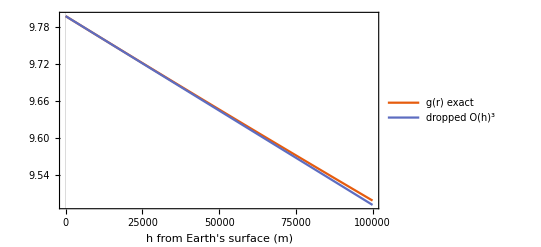

```mathematica
h0=0;
Plot[{(G ME)/(RE+h0+h)^2,G ME(1/(RE+h0)^2-2/(RE+h0)^3(h-h0))},{h,0,100000},PlotLegends->{"g(r) exact","dropped O(h)^3"},PlotTheme->"Scientific",FrameLabel->"h from Earth's surface (m)"]
```

Differential measurement of gravity with two atom interferometers which start out at different heights and therefore accumulate difference phases. The splitting, redirecting, and recombination pulses occur at the same time (lab-frame ) for each cloud.

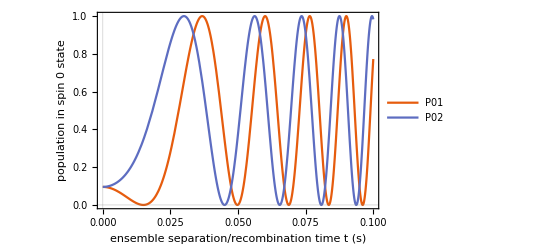

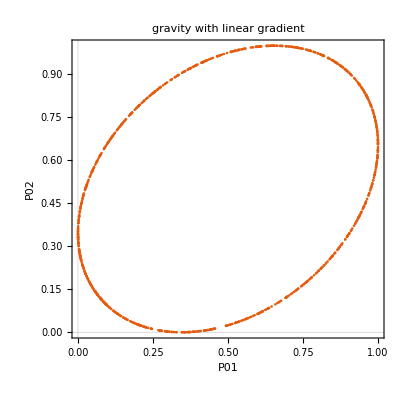

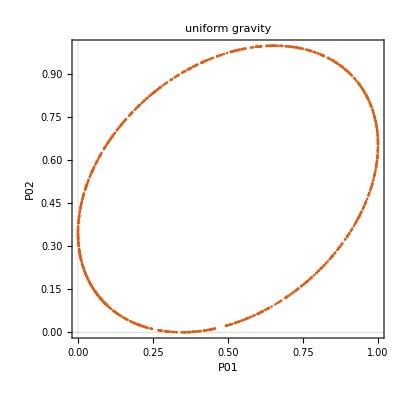

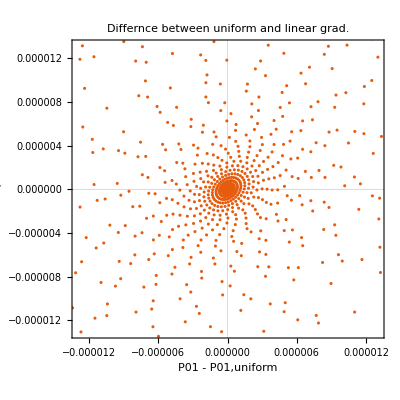

```mathematica
(*two atom interferometers with realistic gravity*)
h1=0.6;(*starting height of ensemble 1*)
h2=0.9;(*starting height of ensemble 2*)
psi0={1,0};(*spin state basis*)
A[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}};
T[x_]:={{Exp[-ⅈ k x],0},{0,Exp[ⅈ k x]}};
(*phase from wave packet traveling in interferometer "arm"*)
Clear[g,k,h0];
k=2π*6.8*^9/(3*^8);
x=1/2(G ME)/(RE+h0)^2 t^2+h0;
(*distance traveled taking into account the acceleration due to gravity, in the momentum kick frame*)
psi=A[π/2].T[-x/.h0->h1].A[π].T[x/.h0->h1].A[π/2].psi0;
P01uniform=(psi0.psi)(psi0.psi)/.{ⅈ->-ⅈ,-ⅈ->ⅈ};
psi=A[π/2].T[-x/.h0->h2].A[π].T[x/.h0->h2].A[π/2].psi0;
P02uniform=(psi0.psi)((psi0.psi)/.{ⅈ->-ⅈ,-ⅈ->ⅈ});
Clear[g,k,h0];
k=2π*6.8*^9/(3*^8);
x=1/2(G ME)/(RE+h0)^2 t^2-(2G ME)/(RE+h0)^3 t^3+h0;
(*distance traveled taking into account the acceleration and jerk due to gravity, in the momentum kick frame*)
psi=A[π/2].T[-x/.h0->h1].A[π].T[x/.h0->h1].A[π/2].psi0;
P01=(psi0.psi)(psi0.psi)/.{ⅈ->-ⅈ,-ⅈ->ⅈ};
psi=A[π/2].T[-x/.h0->h2].A[π].T[x/.h0->h2].A[π/2].psi0;
P02=(psi0.psi)((psi0.psi)/.{ⅈ->-ⅈ,-ⅈ->ⅈ});
Plot[{P01,P02},{t,0,0.1},PlotLegends->{"P01","P02"},PlotTheme->"Scientific",FrameLabel->{"ensemble separation/recombination time t (s)","population in spin 0 state"}]
tf =0.3;
tpts=Range[0,tf,tf/1000];
ListPlot[Transpose@{P01/.t->tpts,P02/.t->tpts},PlotTheme->"Scientific",FrameLabel->{"P01","P02"},AspectRatio->1,PlotLabel->"gravity with linear gradient"]
ListPlot[Transpose@{P01uniform/.t->tpts,P02uniform/.t->tpts},PlotTheme->"Scientific",FrameLabel->{"P01","P02"},AspectRatio->1,PlotLabel->"uniform gravity"]
ListPlot[{Transpose@{P01uniform/.t->tpts,P02uniform/.t->tpts}-Transpose@{P01/.t->tpts,P02/.t->tpts}},PlotTheme->"Scientific",FrameLabel->{"P01 - P01,uniform","P02 - P02,uniform"},AspectRatio->1,PlotLabel->"Differnce between uniform and linear grad."]
(*ParametricPlot[{P01,P02},{t,0,0.1},PlotTheme->"Scientific",FrameLabel->{"P01","P02"}]*)
```

```mathematica
ListPlot[Transpose@{P01uniform/.t->tpts,P02uniform/.t->tpts},PlotTheme->"Scientific",FrameLabel->{"P01","P02"},AspectRatio->1]
```

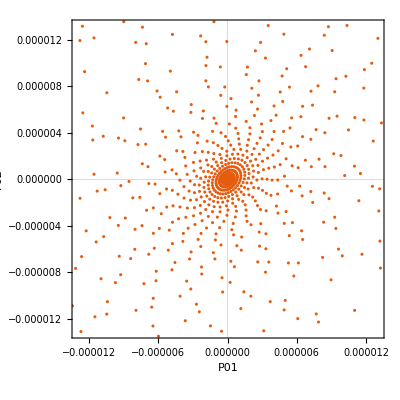

```mathematica
ListPlot[{Transpose@{P01uniform/.t->tpts,P02uniform/.t->tpts}-Transpose@{P01/.t->tpts,P02/.t->tpts}},PlotTheme->"Scientific",FrameLabel->{"P01","P02"},AspectRatio->1]
```

Tests

```mathematica
Clear[h0]
Series[1/(R+h)^2,{h,h0,3}]
```

1/(h0+R)^2-(2 (h-h0))/(h0+R)^3+(3 (h-h0)^2)/(h0+R)^4-(4 (h-h0)^3)/(h0+R)^5+O[h-h0]^4

```mathematica
NSolve[k 1/2(G ME)/(RE+h0)^2 t^2-(2G ME)/(RE+h0)^3 t^3+h0;/.h0->0 ==π,t]
```

{}

pulse time to get π/2, π phase one of the ensembles

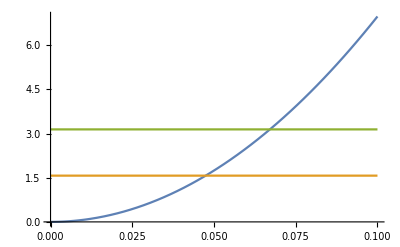

the travel time in the interferometer should not be long enough for the atoms to fall to the launch location

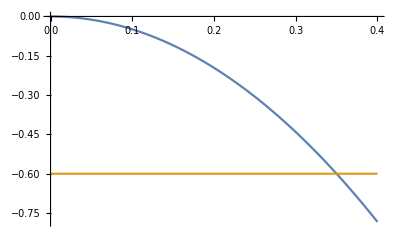

```mathematica
"pulse time to get π/2, π phase one of the ensembles"
Plot[{k 1/2(G ME)/(RE+h0)^2 t^2-(2G ME)/(RE+h0)^3 t^3/.h0->0.6,π/2,π},{t,0,0.1}]
"the travel time in the interferometer should not be long enough for the atoms to fall to the launch location"
Plot[{-(1/2(G ME)/(RE+h0)^2 t^2-(2G ME)/(RE+h0)^3 t^3)/.h0->0.6,-0.6},{t,0,0.4}]
```